```mathematica
translate=Function[s,{s[[1]]+s[[2]],s[[2]]}];
leftColision=Function[s,If[
s[[1,1]]>=0,
s,
{s[[1]]*{-1,1},s[[2]]*{-1,1}}]
];
flipH=Function[s,
{
{1,0}-s[[1]],
{-1,1}*s[[2]]
}
];
flipD=s↦{{s[[1,2]],s[[1,1]]},{s[[2,2]],s[[2,1]]}};
rightColision=flipH@*leftColision@*flipH;
bottomColision=flipD@*leftColision@*flipD;
topColision=flipD@*rightColision@*flipD;
wallColision=Composition[leftColision,rightColision,bottomColision,topColision];
update=Composition[wallColision,translate];
```

```mathematica
state={{0.5,0.7},{0.01,-0.01}}
rate=1/60.;
Dynamic[ListPlot[{state[[1]]},PlotRange->{{0,1},{0,1}},AspectRatio->1,Frame->True]]
Dynamic[state]
While[True,state=update[state];Pause[rate]];
```

```mathematica
f={θ,θdot}↦{θdot,-Sin[θ]}
Grad[f[θ,θdot],{θ,θdot}]
%/.{θ->0}//MatrixForm
%%/.{θ->π}//MatrixForm
```

Function[{θ,θdot},{θdot,-Sin[θ]}]

{{0,1},{-Cos[θ],0}}

(0 | 1
-1 | 0)

(0 | 1
1 | 0)

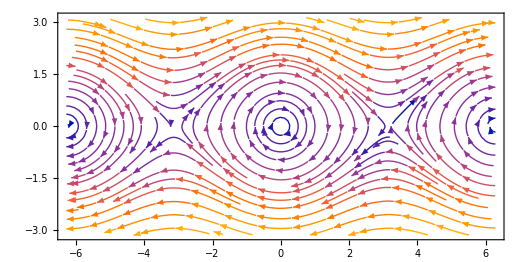

```mathematica
vp=StreamPlot[f[θ,θdot],{θ,-2π,2π},{θdot,-π,π},AspectRatio->1/2,StreamPoints->Fine]
```

```mathematica
eulerForward={f,h}↦s↦s+h Apply[f,s];
wrap=x↦Mod[x+2π,4π]-2π;
```

```mathematica
update=eulerForward[f,0.02];
state={π/4,0};
fps=60.*10;
Dynamic@ListPlot[{{0,0},{Sin[state[[1]]],-Cos[state[[1]]]}},Joined->True,PlotRange->{{-1.1,1.1},{-1.1,1.1}},AspectRatio->1]
Dynamic@Show[vp,Epilog->Point[{wrap[state[[1]]],state[[2]]}]]
Dynamic@state
While[True,state=update[state];Pause[1/fps]];
```